```mathematica
D[x^(x-a)+y^(y+a),a]
```

-x^(-a+x) Log[x]+y^(a+y) Log[y]

```mathematica
f=D[%,a]
```

x^(-a+x) Log[x]^2+y^(a+y) Log[y]^2

```mathematica
Manipulate[Plot[(x+a)^x+(y-a)^y-x^x-y^y,{a,-1,1},PlotRange->{{-0.2,0.2},{-0.02,0.02}}],{x,0.1,1},{y,0.1,1}]
```

```mathematica
0.96^0.96-0.38^0.38//N
```

0.269231

```mathematica
D[(x+a)^x+(y-a)^y,a]
```

x (a+x)^(-1+x)-y (-a+y)^(-1+y)

```mathematica
Manipulate[Plot[%,{a,-1,1},PlotRange->{{-1,1},{-1,1}}],{x,0.1,1},{y,0.1,1}]
```

```mathematica
f=D[%%,a]
```

(-1+x) x (a+x)^(-2+x)+(-1+y) y (-a+y)^(-2+y)

```mathematica
Manipulate[Plot[%,{a,-1,1},PlotRange->{{-1,1},{-10,0}}],{x,0.1,1},{y,0.1,1}]
```

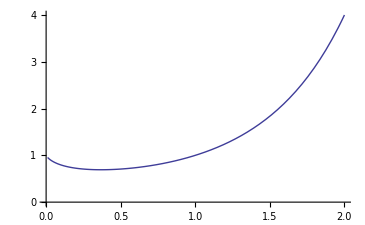

```mathematica
Plot[x^x,{x,0.01,2},PlotRange->{{0,2},{0,4}}]
```

```mathematica
g[x_,y_]:=x^x+y^y-x^y-y^x
```

```mathematica
Plot3D[g[x,y],{x,0.1,10},{y,0.1,10}]
```

-Graphics3D-

```mathematica
h=D[g[x,y],x]
```

-x^(-1+y) y+x^x (1+Log[x])-y^x Log[y]

```mathematica
Plot3D[h,{x,0.1,10},{y,0.1,10}]
```

-Graphics3D-

```mathematica
fch[u_,v_]:=(u+v)^(u+v)+(u-v)^(u-v)-(u+v)^(u-v)-(u-v)^(u+v)
```

```mathematica
D[fch[u,v],v]//Simplify
D[%,v]//Simplify
Manipulate[Plot[%,{v,-5,5},PlotRange->{{-5,5},{0,20}}],{u,0.1,10}]
```

-(u-v)^(u-v) (1+Log[u-v])+(u-v)^(-1+u+v) (u+v+(-u+v) Log[u-v])+(u+v)^(u+v) (1+Log[u+v])+(u+v)^(-1+u-v) (-u+v+(u+v) Log[u+v])

(u-v)^(-1+u-v)+(u+v)^(-1+u+v)+(u-v)^(u-v) (1+Log[u-v])^2+(u-v)^(-1+u+v) (2+Log[u-v])+(u-v)^(-1+u+v) (-(-1+u+v)/(u-v)+Log[u-v]) (u+v+(-u+v) Log[u-v])+(u+v)^(u+v) (1+Log[u+v])^2+(u+v)^(-1+u-v) (2+Log[u+v])-(u+v)^(-2+u-v) (-u+v+(u+v) Log[u+v]) (1-u+v+(u+v) Log[u+v])